# Components of variability

We want to articulate how changing components of temperature vs supply (since we are drawing both from a distribution) change R0 / phi

## Parameters & Helpers

```mathematica
(* ----------------------------------------------------------------------- *)
(* 00  Directory helpers                                                   *)
(* ----------------------------------------------------------------------- *)
Off[General::munfl] 
(* main figure directory (relative to this notebook) *)
figDir = FileNameJoin[{NotebookDirectory[], "..", "..", "figs", "si", 
                       "s-vs-t-variability"}];
If[! DirectoryQ[figDir], 
  CreateDirectory[figDir, CreateIntermediateDirectories -> True]];

(* data directory for binary objects *)
dataDir = FileNameJoin[{NotebookDirectory[], "..", "..", "outputs", 
                        "intermediate-obs", "s-vs-t-variability"}];
If[! DirectoryQ[dataDir], 
  CreateDirectory[dataDir, CreateIntermediateDirectories -> True]];

(* ----------------------------------------------------------------------- *)
(* 01  Environmental response functions                                    *)
(* ----------------------------------------------------------------------- *)

ClearAll[ImaxFunc, RespirationFunc, SuitabilityFunc];

(* TODO: adjust TI / gamma for species-specific thermal curve *)
ImaxFunc[T_, TI_, gamma_] := Exp[-((T - TI)^2)/gamma];

(* TODO: refine metabolic parameters ma, mb, mc *)
RespirationFunc[T_, {ma_, mb_, mc_}] := ma*Exp[mb*T] + mc;

SuitabilityFunc[T_, S_, params_Association] :=
 Module[{imax, m},
   imax = ImaxFunc[T, params["TI"], params["gamma"]];
   m    = RespirationFunc[T, params["mParams"]];
   Max[0, (imax*S)/(S + params["Shalf"]) - m]
 ];

(* ----------------------------------------------------------------------- *)
(* 02  Landscape generator                                                 *)
(* ----------------------------------------------------------------------- *)

ClearAll[MakeLandscape];

MakeLandscape[nPatches_, meanT_, varT_, meanS_, varS_, suitParams_] :=
 Module[{temps, supp, wRaw, wNorm},
   temps = RandomVariate[NormalDistribution[meanT, varT], nPatches];
   supp  = RandomVariate[NormalDistribution[meanS, varS], nPatches];
   wRaw  = MapThread[SuitabilityFunc[#1, #2, suitParams] &, {temps, supp}];
   wNorm = wRaw/Total[wRaw]; (* ensure ∑ w_i = 1 *)
   AssociationThread[
     Range[nPatches],
     MapThread[<|"T" -> #1, "S" -> #2, "w" -> #3|> &, {temps, supp, wNorm}]
   ]
 ];

(* ----------------------------------------------------------------------- *)
(* 03  Patch-level φ and landscape-level R0                                *)
(* ----------------------------------------------------------------------- *)

ClearAll[PatchPhi, PhiLandscape];

PhiI[Stotal_, patch_, epsF_] :=
  Module[{w = patch["w"], eps = epsF[patch["T"]]},
    eps * w * (1 - (1 - w)^Stotal)
  ];

(* R0 = Σ Φ_i over all patches *)
R0fromLandscape[landscape_Association, Stotal_, epsF_] :=
  Total[PhiI[Stotal, #, epsF] & /@ Values[landscape]];

(* ----------------------------------------------------------------------- *)
(* 04  ε(T) constructor (scalar or function)                               *)
(* ----------------------------------------------------------------------- *)

ClearAll[MakeEpsilonFunc];

MakeEpsilonFunc[epsSpec_] :=
  If[NumericQ[epsSpec],
     Function[{T}, epsSpec],   (* constant transmission prob *)
     epsSpec                   (* already a function *)
  ];

(* TODO: choose one of the following definitions *)
epsFunc = MakeEpsilonFunc[1];                                        (* constant 1 *)
(* epsFunc = MakeEpsilonFunc[0.3];                                   (* constant 0.3 *) *)
(* epsFunc = MakeEpsilonFunc[Function[{T}, 1/(1 + Exp[-0.25 (T - 22)])]]; *)

(* ----------------------------------------------------------------------- *)
(* 05  Global simulation parameters                                        *)
(* ----------------------------------------------------------------------- *)

(* heterogeneity grid *)
sigmaTList  = Range[0.0001, 5, 0.5];     (* TODO: widen or narrow grid *)
sigmaSList  = Range[0.0001, 3, 0.5];

(* suitability-function constants *)
suitParams = <|
  "TI"     -> 25, (* Optimal temperature *)
  "gamma"  -> 150, (* Temperature response breadth *)
  "Shalf"  -> 0.5,
  "mParams"-> {0.05, 0.1, 0.05}
|>;

(* fixed means for temperature & supply *)
meanT = 22;        (* °C *)
varT  = 1;         (* TODO: confirm this is SD, not variance        *)
meanS = 0.8;        (* resource units *)
varS  = 0.2;

(* 
All needed parameters:
- nReps
- nPatches
- sTotal
- varR
- meanR
- varT
- meanT
- optT
- rHalf
- mParams
- respBreadth
- epsF
- 

*)
```

## How does increasing heterogeneity in T and R change the basic reproduction number R0​?

```mathematica
(* ======================================================================= *)
(* 06  Full run for a list of ε(T) definitions                             *)
(* ======================================================================= *)

nReplicates = 10;      (* how many landscapes per grid point            *)
nPatches    = 2000;  (* patches in each landscape                     *)
Stotal      = 1500;  (* total susceptibles on the whole landscape     *)

(* ---------- message hygiene ------------------------------------------- *)
ParallelEvaluate[Off[General::munfl]];
Off[General::munfl];

(* ---------- list of ε specs ------------------------------------------- *)
epsConfigs = {
  <|"label" -> "eps1.0",      "func" -> MakeEpsilonFunc[1]                             |>,
  <|"label" -> "eps0.3",      "func" -> MakeEpsilonFunc[0.3]                           |>,
  <|"label" -> "epsLogistic", "func" -> MakeEpsilonFunc[
                                      Function[{T}, 1/(1 + Exp[-0.25 (T - 22)])]]     |>,
  <| "label" -> "epsGaussian", "func" -> MakeEpsilonFunc[
                                      Function[{T}, Exp[-((T - 25)^2)/(2 5^2)]]]   |>
};

(* pick slice points for diagnostics *)
sliceSigmaT = {0.1, 0.5, 1, 1.5, 2, 3};
sliceSigmaS = {0.1, 0.5, 1, 1.5, 2, 3};
baselineSigmaT = 1;   baselineSigmaS = 1;

(* ---------- helper: run grid for ONE ε definition --------------------- *)
ClearAll[runGridForEps];
runGridForEps[epsLabel_String, epsF_] :=
 Module[{computeR0, resultGrid, phiMeans, phiSDs, surfaceData, surfacePlot,
         phiSliceT, phiSliceS, plotT, plotS, sliceGrid},

  (* --- numerics for one σ_T, σ_S pair *)
  ClearAll[computeR0];
  computeR0[sigT_, sigS_] :=
    Module[{rVals},
      rVals = Table[
        With[{land = MakeLandscape[nPatches, meanT, sigT,
                                   meanS, sigS, suitParams]},
          PhiFromLandscape[land, Stotal, epsF]
        ],
        {nReplicates}
      ];
      {Mean[rVals], StandardDeviation[rVals]}
    ];

  Print["###  ε = ", epsLabel, "  – running grid…"];

  resultGrid = ParallelTable[
     computeR0[sigT, sigS],
     {sigT, sigmaTList},
     {sigS, sigmaSList}
  ];

  phiMeans = Map[First, resultGrid, {2}];
  phiSDs   = Map[Last,  resultGrid, {2}];

  (* --- 3-D surface ---------------------------------------------------- *)
  surfaceData = Flatten[
     Table[{sigmaTList[[i]], sigmaSList[[j]], phiMeans[[i, j]]},
           {i, Length[sigmaTList]}, {j, Length[sigmaSList]}],
     1];

  surfacePlot = ListPlot3D[
     surfaceData,
     Mesh          -> None,
     AxesLabel     -> {"σ_T", "σ_S", "E[R0]"},
     ColorFunction -> "TemperatureMap",
     PlotRange     -> All
  ];
  Print[surfacePlot]
  Export[FileNameJoin[{figDir,
          "phi-surface-" <> epsLabel <> ".png"}], surfacePlot, "PNG"];

  (* --- 1-D slices ----------------------------------------------------- *)
  phiSliceT = ParallelMap[First@computeR0[#, baselineSigmaS] &, sliceSigmaT];
  phiSliceS = ParallelMap[First@computeR0[baselineSigmaT, #] &, sliceSigmaS];

  plotT = ListPlot[
     Transpose[{sliceSigmaT, phiSliceT}],
     Joined      -> True, Frame -> True,
     FrameLabel  -> {"σ_T (Temp SD)", "E[R0]"},
     PlotMarkers -> Automatic,
     PlotLabel   -> "Temp variability – " <> epsLabel
  ];

  plotS = ListPlot[
     Transpose[{sliceSigmaS, phiSliceS}],
     Joined      -> True, Frame -> True,
     FrameLabel  -> {"σ_S (Supply SD)", "E[R0]"},
     PlotMarkers -> Automatic,
     PlotLabel   -> "Supply variability – " <> epsLabel
  ];

  sliceGrid = GraphicsGrid[{{plotT, plotS}}, Spacings -> {2, 1}];

  Export[FileNameJoin[{figDir,
          "phi-slices-" <> epsLabel <> ".png"}], sliceGrid, "PNG"];

  (* --- save numeric arrays ------------------------------------------- *)
  Export[FileNameJoin[{dataDir, "phiMeans-" <> epsLabel <> ".mx"}],
         phiMeans, "MX"];
  Export[FileNameJoin[{dataDir, "phiSDs-"   <> epsLabel <> ".mx"}],
         phiSDs,   "MX"];
];

(* ---------- main loop over all ε(T) versions -------------------------- *)
Do[
  runGridForEps[conf["label"], conf["func"]],
  {conf, epsConfigs}
];

Print["#### All ε grids finished.  Outputs written to figDir & dataDir."];
```

###  ε = eps1.0  – running grid…

-Graphics3D-

###  ε = eps0.3  – running grid…

-Graphics3D-

###  ε = epsLogistic  – running grid…

-Graphics3D-

###  ε = epsGaussian  – running grid…

-Graphics3D-

#### All ε grids finished.  Outputs written to figDir & dataDir.

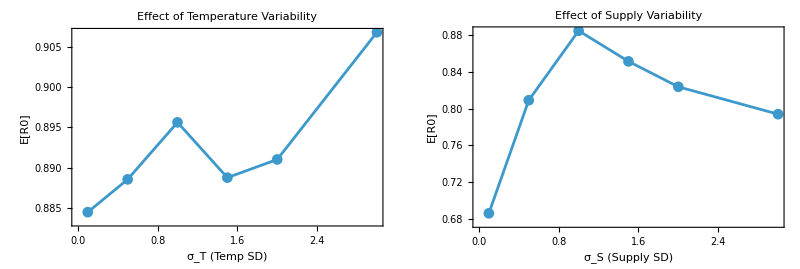

```mathematica
(* ----------------------------------------------------------------------- *)
(* 06b  1-D sensitivity plots: σ_T slice vs σ_S slice                       *)
(* ----------------------------------------------------------------------- *)

(* --- choose slice points ---------------------------------------------- *)
sliceSigmaT = {0.1, 0.5, 1, 1.5, 2, 3};             (* TODO: tweak *)
sliceSigmaS = {0.1, 0.5, 1, 1.5, 2, 3};             (* TODO: tweak *)

(* fixed baseline values (centre of other axis) *)
baselineSigmaT = 1;      (* held constant while σ_S varies *)
baselineSigmaS = 1;      (* held constant while σ_T varies *)

(* --- recalc R0 means on each slice ------------------------------------ *)
phiSliceT = ParallelMap[
   First @ computeR0[#, baselineSigmaS] &,
   sliceSigmaT
];

phiSliceS = ParallelMap[
   First @ computeR0[baselineSigmaT, #] &,
   sliceSigmaS
];

(* --- build two simple line plots -------------------------------------- *)
plotT = ListPlot[
   Transpose[{sliceSigmaT, phiSliceT}],
   Joined       -> True,
   Frame        -> True,
   FrameLabel   -> {"σ_T (Temp SD)", "E[R0]"},
   PlotMarkers  -> Automatic,
   PlotLabel    -> "Effect of Temperature Variability",
   ImageSize    -> Medium
];

plotS = ListPlot[
   Transpose[{sliceSigmaS, phiSliceS}],
   Joined       -> True,
   Frame        -> True,
   FrameLabel   -> {"σ_S (Supply SD)", "E[R0]"},
   PlotMarkers  -> Automatic,
   PlotLabel    -> "Effect of Supply Variability",
   ImageSize    -> Medium
];

sliceGrid = GraphicsGrid[{{plotT, plotS}}, Spacings -> {2, 1}]

(* --- export ----------------------------------------------------------- *)
Export[
  FileNameJoin[{figDir, "phi-sensitivity-slices.png"}],
  sliceGrid,
  "PNG"
];

(* TODO: add error bars with phiSDs if we like; tweak slice values;        *)
(*       or normalise curves to their baseline R0 for relative change.     *)
```

## Trying to get a minimal version of a simulation to define a TPC, define a transmission curve, and see how that changes R0

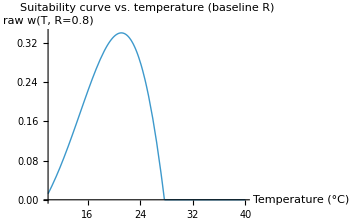

```mathematica
Rbaseline = 0.8;          (* = 0.8 by default *)
(* temperature range to sweep *)
Tmin = 10;  Tmax = 40;
suitParams["Shalf"] = 0.1;

wCurve = Plot[
  SuitabilityFunc[T, Rbaseline, suitParams],
  {T, Tmin, Tmax},
  PlotRange   -> All,
  AxesLabel   -> {"Temperature (°C)", "raw w(T, R=0.8)"},
  PlotLabel   -> "Suitability curve vs. temperature (baseline R)",
  PlotStyle   -> Thick,
  ImageSize   -> Medium
]
```

{0.0460125,0.658086,0.}

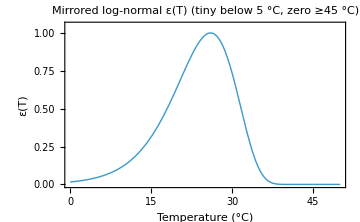

```mathematica
ClearAll[epsMirrorLogNorm];

Topt     = 26.;           (* optimum transmission temperature            *)
TcutOff  = 45.;           (* ε(T) = 0 for T ≥ TcutOff                    *)
sigmaLN  = 0.3;           (* breadth of the log-normal (play with this)  *)

(* Step 1.  Work in the mirrored variable  Y = TcutOff - T  ( > 0 below cutoff) *)
(*          We want Y_mode = TcutOff - Topt  so the mode maps back to Topt.   *)
yMode    = TcutOff - Topt;
muLN     = Log[yMode] + sigmaLN^2;         (* sets mode at yMode            *)

(* Step 2.  Unscaled ε(T) for  0 < Y < ∞   but we will zero it for T ≥ TcutOff *)
epsRaw[T_] :=
  If[T >= TcutOff,
     0.,
     1/((TcutOff - T)*sigmaLN*Sqrt[2 Pi]) *
       Exp[-(Log[TcutOff - T] - muLN)^2/(2 sigmaLN^2)]
  ];

(* Step 3.  Scale so ε(Topt) = 1 *)
scaleFactor   = 1/epsRaw[Topt];
epsMirrorLogNorm[T_] := scaleFactor*epsRaw[T];

(* ----------------------------------------------------------------------- *)
(* quick sanity check and plot                                             *)
(* ----------------------------------------------------------------------- *)
{epsMirrorLogNorm[5], epsMirrorLogNorm[20], epsMirrorLogNorm[45]}
(* -> {≈0.03, 1., 0.}  — small at 5 °C, 1 at optimum, 0 at ≥45 °C *)

mirrorPlot = Plot[
  epsMirrorLogNorm[T], {T, 0, 50},
  PlotStyle  -> Thick,
  PlotRange  -> {0, 1.05},
  Frame      -> True,
  FrameLabel -> {"Temperature (°C)", "ε(T)"},
  PlotLabel  -> "Mirrored log-normal ε(T)\n(tiny below 5 °C, zero ≥45 °C)",
  ImageSize  -> Medium
]
```

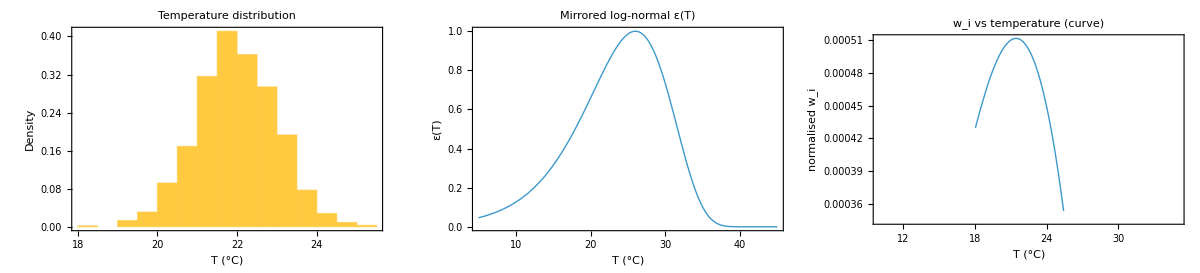

=== diagnostic summary ====================================

patches (n)              : 2000

env mean T (°C)          : 22

env sd   T (°C)          : 1

supply per patch (R)     : 5

total susceptibles       : 3000

peak w at T =            : 21.4

ΔT  (T_peak - μ_T)       : -0.6

E[R0] for this landscape : 0.63

png saved   → /Users/colebrookson/github/theRmal-landscape/src/mathematica/../../figs/si/s-vs-t-variability/singleLandscape_diagnostics.png

===========================================================

```mathematica
(* ----------------------------------------------------------------------- *)
(* parameters                                                              *)
(* ----------------------------------------------------------------------- *)
nPatchesDiag   = 2000;
muTLand        = 22;            sdTLand  = 1;      (* °C *)
supplyMu = 0.8;        (* resource units *)
supplySD  = 0.2;
StotalDiag     = 3000;                            (* total susceptibles *)
supplyConst = 5;
(* ----------------------------------------------------------------------- *)
(* draw one landscape                                                      *)
(* ----------------------------------------------------------------------- *)
temps   = RandomVariate[NormalDistribution[muTLand, sdTLand], nPatchesDiag];
(*supply  = RandomVariate[NormalDistribution[supplyMu, supplySD], nPatchesDiag];*)
supply  = ConstantArray[supplyConst, nPatchesDiag];
wRaw    = MapThread[SuitabilityFunc[#1, #2, suitParams] &, {temps, supply}];
wNorm   = wRaw/Total[wRaw];                       (* Σ w_i = 1           *)

(* mirrored log-normal ε(T) from previous step *)
epsF     = epsMirrorLogNorm;
epsVals  = epsF /@ temps;

(* ----------------------------------------------------------------------- *)
(* compute R0, T_peak, ΔT                                                  *)
(* ----------------------------------------------------------------------- *)
phiList = epsVals * wNorm * (1 - (1 - wNorm)^StotalDiag);
R0Diag  = Total[phiList];

Tpeak   = temps[[First@Ordering[wNorm, -1]]];
deltaT  = Tpeak - muTLand;

(* ----------------------------------------------------------------------- *)
(* plotting                                                               *)
(* ----------------------------------------------------------------------- *)
histT = Histogram[
  temps, 20, "PDF",
  Frame -> True,
  FrameLabel -> {"T (°C)", "Density"},
  PlotLabel  -> "Temperature distribution",
  ImageSize  -> Medium
];

epsPlot = Plot[
  epsF[T], {T, 5, 45},
  Frame      -> True,
  FrameLabel -> {"T (°C)", "ε(T)"},
  PlotLabel  -> "Mirrored log-normal ε(T)",
  PlotStyle  -> Thick,
  ImageSize  -> Medium
];

{tempsSorted, wNormSorted} = Transpose@SortBy[Transpose[{temps, wNorm}], First];

wCurve = ListLinePlot[
  Transpose[{tempsSorted, wNormSorted}],
  Frame      -> True,
  PlotRange   -> {{10, 35}, All},        (* ← x-axis explicitly 10–35 °C *)
  FrameLabel -> {"T (°C)", "normalised w_i"},
  PlotStyle  -> Thick,
  PlotLabel  -> "w_i vs temperature (curve)",
  ImageSize  -> Medium
];

diagGrid = GraphicsGrid[{{histT, epsPlot, wCurve}}, Spacings -> {2, 1}]

Export[
  FileNameJoin[{figDir, "singleLandscape_diagnostics.png"}],
  diagGrid, "PNG"
];

(* ----------------------------------------------------------------------- *)
(* console summary                                                         *)
(* ----------------------------------------------------------------------- *)
Print /@ {
  "=== diagnostic summary ====================================",
  "patches (n)              : " <> ToString[nPatchesDiag],
  "env mean T (°C)          : " <> ToString[muTLand],
  "env sd   T (°C)          : " <> ToString[sdTLand],
  "supply per patch (R)     : " <> ToString[supplyConst],
  "total susceptibles       : " <> ToString[StotalDiag],
  "peak w at T =            : " <> ToString@NumberForm[Tpeak, {3,1}],
  "ΔT  (T_peak - μ_T)       : " <> ToString@NumberForm[deltaT, {3,1}],
  "E[R0] for this landscape : " <> ToString@NumberForm[R0Diag, {4,2}],
  "png saved   → " <> FileNameJoin[{figDir, "singleLandscape_diagnostics.png"}],
  "==========================================================="
};
```

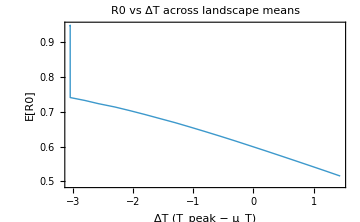

### ΔT sweep complete – plot & table saved to figDir/dataDir.

```mathematica
(* ======================================================================= *)
(* 10  ΔT sweep: vary landscape mean temp, record R0 and ΔT                *)
(* ======================================================================= *)

(* ----------------------------------------------------------------------- *)
(* user knobs                                                              *)
(* ----------------------------------------------------------------------- *)
muRange        = Range[20, 30, 0.25];   (* env means to test                *)
nRepsPerMu     = 10;                  (* Monte-Carlo reps per μ_T         *)
seedBase       = 123;                (* for reproducibility; change/omit *)
(* supplyConst, nPatchesDiag, StotalDiag, sdTLand already in memory       *)

(* ----------------------------------------------------------------------- *)
(* helper to produce one {ΔT, R0} for a given μ_T                          *)
(* ----------------------------------------------------------------------- *)
ClearAll[R0forMu];
R0forMu[mu_, repID_] :=
 BlockRandom[                               (* reproducible RNG per rep *)
  RandomSeed[seedBase + repID];             (* different seed each loop *)
  Module[{temps, supply, wRaw, wNorm, epsVals,
          phiList, R0, Tpeak, deltaT},
    temps   = RandomVariate[NormalDistribution[mu, sdTLand], nPatchesDiag];
    supply  = ConstantArray[supplyConst, nPatchesDiag];
    wRaw    = MapThread[SuitabilityFunc[#1, #2, suitParams] &, {temps, supply}];
    wNorm   = wRaw/Total[wRaw];
    epsVals = epsMirrorLogNorm /@ temps;

    phiList = epsVals*wNorm*(1 - (1 - wNorm)^StotalDiag);
    R0      = Total[phiList];

    Tpeak   = temps[[First@Ordering[wNorm, -1]]];
    deltaT  = Tpeak - mu;

    {deltaT, R0}
  ]
];

(* ----------------------------------------------------------------------- *)
(* run sweep                                                               *)
(* ----------------------------------------------------------------------- *)
results = Table[
   Mean[Table[R0forMu[mu, r], {r, nRepsPerMu}]],     (* mean over reps *)
   {mu, muRange}
];

deltaTvals = results[[All, 1]];
R0vals     = results[[All, 2]];

(* save numeric table *)
Export[
  FileNameJoin[{dataDir, "R0_vs_deltaT_table.mx"}],
  Transpose[{muRange, deltaTvals, R0vals}], "MX"
];

(* ----------------------------------------------------------------------- *)
(* plot                                                                    *)
(* ----------------------------------------------------------------------- *)
deltaPlot = ListLinePlot[
  Transpose[{deltaTvals, R0vals}],
  Frame      -> True,
  FrameLabel -> {"ΔT (T_peak − μ_T)", "E[R0]"},
  Joined     -> True,
  PlotStyle  -> Thick,
  PlotLabel  -> "R0 vs ΔT across landscape means",
  ImageSize  -> Medium
]

Export[
  FileNameJoin[{figDir, "R0_vs_deltaT_sweep.png"}],
  deltaPlot, "PNG"
];

Print["### ΔT sweep complete – plot & table saved to figDir/dataDir."]
```

```mathematica
(* ======================================================================= *)
(* 08  Mismatch experiment: fixed σ_T, sweeping μ_T                        *)
(* ======================================================================= *)

(* ----------------------------------------------------------------------- *)
(* 8.1  experiment-specific parameters                                     *)
(* ----------------------------------------------------------------------- *)

Topt        = 25;          (* species’ thermal optimum                   *)
sigmaTPC    = 5;           (* breadth of TPC                             *)
sigmaT_fixed = 1;          (* SD of environmental temperature            *)
muTList     = Range[10, 40, 1];    (* env means to sweep                 *)

(* gaussian TPC: peak = 1 at Topt *)
epsTPC = MakeEpsilonFunc[
   Function[{T}, Exp[-((T - Topt)^2)/(2 sigmaTPC^2)]]
];

(* ----------------------------------------------------------------------- *)
(* 8.2  helper: constant ε that matches mean of gaussian under env distro  *)
(* ----------------------------------------------------------------------- *)
ClearAll[meanTPCunderEnv];
meanTPCunderEnv[mu_] :=
  NExpectation[
    epsTPC[TT],                                 (* integrand   *)
    {TT, NormalDistribution[mu, sigmaT_fixed]}  (* variable & dist *)
  ];

(* ----------------------------------------------------------------------- *)
(* 8.3  compute R0 curves for TPC vs constant                              *)
(* ----------------------------------------------------------------------- *)
ClearAll[R0_mismatch];

R0_mismatch[epsF_, mu_] :=
 Module[{land},
   land = MakeLandscape[nPatches, mu, sigmaT_fixed, meanS, varS, suitParams];
   PhiFromLandscape[land, Stotal, epsF]
 ];

(* --- build vectors ----------------------------------------------------- *)
deltaT      = muTList - Topt;
R0_TPC      = ParallelMap[R0_mismatch[epsTPC, #] &, muTList];

epsConstVec = meanTPCunderEnv /@ muTList;
epsConstFun[epsc_] := Function[{T}, epsc];

R0_const = MapThread[
   R0_mismatch[epsConstFun[#2], #1] &,          (* #1 = μ_T, #2 = ε_const *)
   {muTList, epsConstVec}
];
(* save data for later *)
Export[FileNameJoin[{dataDir, "R0_mismatch_curves.mx"}],
       {deltaT, R0_TPC, R0_const}, "MX"];

(* ----------------------------------------------------------------------- *)
(* 8.4  plotting                                                           *)
(* ----------------------------------------------------------------------- *)

(* -- Panel A: TPC curve and env means ---------------------------------- *)
tpcPlot = Plot[
  epsTPC[T], {T, 10, 40},
  PlotStyle -> Thick,
  AxesLabel -> {"Temperature (°C)", "ε_TPC"},
  PlotLabel -> "Thermal performance curve & env means"
];

meanLines = Graphics[
  Table[{Gray, Dashed, Line[{{mu, 0}, {mu, epsTPC[mu]}}]}, {mu, muTList}]
];

tpcPanel = Show[tpcPlot, meanLines, ImageSize -> Medium];

Export[FileNameJoin[{figDir, "tpc_with_means.png"}], tpcPanel, "PNG"];

(* -- Panel B: R0 vs ΔT for TPC kernel ---------------------------------- *)
plotTPC = ListLinePlot[
  Transpose[{deltaT, R0_TPC}],
  Frame      -> True,
  FrameLabel -> {"ΔT = μ_T - T_opt", "E[R0]"},
  Joined     -> True,
  PlotStyle  -> Blue,
  PlotLabel  -> "R0 vs ΔT (Gaussian ε)"
];

(* -- Panel C: R0 vs ΔT for constant kernel ----------------------------- *)
plotConst = ListLinePlot[
  Transpose[{deltaT, R0_const}],
  Frame      -> True,
  FrameLabel -> {"ΔT", "E[R0]"},
  Joined     -> True,
  PlotStyle  -> Red,
  PlotLabel  -> "R0 vs ΔT (Constant ε)"
];

mismatchGrid = GraphicsGrid[
  {{plotTPC, plotConst}},
  Spacings -> {2, 1}
];

Export[FileNameJoin[{figDir, "R0_mismatch_curves.png"}],
       mismatchGrid, "PNG"];

Print["###  mismatch experiment finished – outputs saved to figDir/dataDir."];
```

Rule::rhs: Pattern R0_mismatch appears on the right-hand side of rule R0_TPC→{R0_mismatch[Function[{T},Exp[-Power[«2»]/Times[«2»]]],10],R0_mismatch[Function[{T},Exp[-Power[«2»]/Times[«2»]]],11],R0_mismatch[Function[{T},Exp[-Power[«2»]/Times[«2»]]],12],«26»,R0_mismatch[Function[{T},Exp[-Power[«2»]/Times[«2»]]],39],R0_mismatch[Function[{T},Exp[-Power[«2»]/Times[«2»]]],40]}.

General::stop: Further output of Rule::rhs will be suppressed during this calculation.

NExpectation::input: Invalid input.

General::stop: Further output of NExpectation::input will be suppressed during this calculation.

Rule::rhs: Pattern R0_mismatch appears on the right-hand side of rule R0_const→{R0_mismatch[Function[{T$},NExpectation[ⅇ^(-1/50 Power[«2»]),{TT,NormalDistribution[10,Pattern[«2»]]}]],10],R0_mismatch[Function[{T$},NExpectation[ⅇ^(-1/50 Power[«2»]),{TT,NormalDistribution[11,Pattern[«2»]]}]],11],«28»,R0_mismatch[Function[{T$},NExpectation[ⅇ^(-1/50 Power[«2»]),{TT,NormalDistribution[40,Pattern[«2»]]}]],40]}.

General::stop: Further output of Rule::rhs will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {{-15,-14,-13,-12,-11,-10,-9,-8,-7,-6,-5,-4,-3,-2,-1,0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},R0_TPC} cannot be transposed.

Transpose::nmtx: The first two levels of {{-15.,-14.,-13.,-12.,-11.,-10.,-9.,-8.,-7.,-6.,-5.,-4.,-3.,-2.,-1.,0,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.},R0_TPC} cannot be transposed.

Transpose::nmtx: The first two levels of {{-15.,-14.,-13.,-12.,-11.,-10.,-9.,-8.,-7.,-6.,-5.,-4.,-3.,-2.,-1.,0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.},R0_TPC} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Rule::rhs: Pattern R0_TPC appears on the right-hand side of rule System`ListPlotsDump`modelData[WrappedValues,{,Charting`Private`Tag]→{{«1»},«6»}^T.

ListLinePlot::lpn: { is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {{-15,-14,-13,-12,-11,-10,-9,-8,-7,-6,-5,-4,-3,-2,-1,0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},R0_const} cannot be transposed.

Transpose::nmtx: The first two levels of {{-15.,-14.,-13.,-12.,-11.,-10.,-9.,-8.,-7.,-6.,-5.,-4.,-3.,-2.,-1.,0,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.},R0_const} cannot be transposed.

Transpose::nmtx: The first two levels of {{-15.,-14.,-13.,-12.,-11.,-10.,-9.,-8.,-7.,-6.,-5.,-4.,-3.,-2.,-1.,0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.},R0_const} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Rule::rhs: Pattern R0_const appears on the right-hand side of rule System`ListPlotsDump`modelData[WrappedValues,{,Charting`Private`Tag]→(«1»)^T.

ListLinePlot::lpn: { is not a list of numbers or pairs of numbers.

###  mismatch experiment finished – outputs saved to figDir/dataDir.

## Is the gradient steeper along the temperature or resource axis?

## Given a fixed recovery rate γ, how does epidemic peak size vary with R0R0​ when heterogeneity is present? *TODO*

# EXTRA CODE

### Some code I tried to write to make the one part faster but it doesn’t work

```mathematica
Off[General::munfl];           (* silence benign underflow warnings      *)

nReplicates    = 10;           (* TODO: ↑ for smoother means             *)
nPatches       = 20_000;       (* keep high – code is vectorised now     *)
Stotal         = 15_000;       (* total susceptible hosts on landscape   *)

(* === 6.1  compiled suitability  ======================================= *)
With[{TI    = suitParams["TI"],
      γ     = suitParams["gamma"],
      Shalf = suitParams["Shalf"],
      {ma, mb, mc} = suitParams["mParams"]},

  ClearAll[SuitabilityVec];

  SuitabilityVec = Compile[
    {{t, _Real, 1}, {s, _Real, 1}},                 (* argument patterns  *)
    Module[{imax, m},                               (* body               *)
      imax = Exp[-((t - TI)^2)/γ];
      m    = ma*Exp[mb*t] + mc;
      Max[0, (imax*s)/(s + Shalf) - m]
    ],
    RuntimeAttributes -> {Listable}                 (* <-- options here   *)
  ];                                                (* <-- closing ]      *)
];

(* === 6.2  compiled Φ_i  (vectorised, small-w safe) ==================== *)
ClearAll[PhiVec];
PhiVec = Compile[
  {{w, _Real, 1}, {eps, _Real, 1}, {Stot, _Integer}},
  Module[{term},
    term = 1 - (1 - w)^Stot;
    (* if term underflows, switch to first-order approximation S*w *)
    term = If[term < 10.^-8, Stot*w, term];
    eps*w*term
  ],
  RuntimeAttributes -> {Listable}
];

(* === 6.3  per-cell R0 evaluator  ====================================== *)
ClearAll[computeR0Fast];
computeR0Fast[sdT_, sdS_] :=
 Module[{rVals, temps, supp, wNorm, epsList},
   rVals = Table[
     temps = RandomVariate[NormalDistribution[meanT, sdT], nPatches];
     supp  = RandomVariate[NormalDistribution[meanS, sdS], nPatches];

     wNorm = SuitabilityVec[temps, supp];
     wNorm = wNorm/Total[wNorm];           (* ensures Σ w_i = 1 *)

     epsList = epsFunc /@ temps;           (* vector of ε(T_i)         *)

     Total@PhiVec[wNorm, epsList, Stotal],
     {nReplicates}
   ];
   {Mean[rVals], StandardDeviation[rVals]}
];

Print["#### Running R0 grid (compiled)…"];

resultGrid = ParallelTable[
   computeR0Fast[sdT, sdS],
   {sdT, sigmaTList},
   {sdS, sigmaSList}
];

Print["#### Grid complete."];

(* === 6.4  unpack & plot ============================================== *)
phiMeans = Map[First, resultGrid, {2}];
phiSDs   = Map[Last,  resultGrid, {2}];

surfaceData = Flatten[
   Table[{sigmaTList[[i]], sigmaSList[[j]], phiMeans[[i, j]]},
         {i, Length[sigmaTList]}, {j, Length[sigmaSList]}],
   1];

surfacePlot = ListPlot3D[
   surfaceData /. {x_, y_, z_} :> {x, y, Log10[z + 10.^-12]},  (* log scale *)
   Mesh          -> None,
   AxesLabel     -> {"σ_T", "σ_S", "log10 E[R0]"},
   ColorFunction -> "TemperatureMap",
   PlotRange     -> All
];

Export[FileNameJoin[{figDir, "phi-response-surface.png"}],
       surfacePlot, "PNG"];

(* same persist-to-MX block as before *)
Export[FileNameJoin[{dataDir, "paramGrid.mx"}],
       Tuples[{sigmaTList, sigmaSList}], "MX"];
Export[FileNameJoin[{dataDir, "phiMeans.mx"}], phiMeans, "MX"];
Export[FileNameJoin[{dataDir, "phiSDs.mx"}],   phiSDs,   "MX"];
```

```mathematica
(*SCRATCH!!!!!*)
(* ----------------------------------------------------------------------- *)
(* 10  Outlier check & plot-range fixes                                    *)
(* ----------------------------------------------------------------------- *)

(* locate extreme values *)
maxR0     = Max[phiMeans];
posMax    = Position[phiMeans, maxR0][[1]];
σTmax     = sigmaTList[[posMax[[1]]]];
σSmax     = sigmaSList[[posMax[[2]]]];

Print[
  "Largest mean R0 = ", ScientificForm[maxR0, 3],
  " at σ_T = ", σTmax, ", σ_S = ", σSmax
];

(* optional: quick histogram to see the magnitude spread *)
Histogram[Flatten[phiMeans], 30, "Log", 
  AxesLabel -> {"E[R0]", "count"}, 
  PlotLabel -> "Distribution of mean R0 values"]

(*(* === PLOT OPTION 1 – clip the upper tail ============================= *)
clipLevel  = Quantile[Flatten[phiMeans], 0.99];   (* TODO: choose quantile *)
surfaceDataClipped = surfaceData /. {x_, y_, z_} :> {x, y, Min[z, clipLevel]};

surfacePlotClip = ListPlot3D[
  surfaceDataClipped,
  Mesh         -> None,
  AxesLabel    -> {"σ_T", "σ_S", "E[R0] (clipped)"},
  PlotRange    -> All,
  ColorFunction-> "TemperatureMap",
  PlotLabel    -> 
   Style[Row[{"Clipped at ", clipLevel // ScientificForm}], 12]
];

Export[FileNameJoin[{figDir, "phi-surface-clipped.png"}],
       surfacePlotClip, "PNG"];

(* === PLOT OPTION 2 – log10 scale on z-axis =========================== *)
surfaceDataLog = surfaceData /. {x_, y_, z_} :> {x, y, Log10[z]};

surfacePlotLog = ListPlot3D[
  surfaceDataLog,
  Mesh         -> None,
  AxesLabel    -> {"σ_T", "σ_S", "log10 E[R0]"},
  PlotRange    -> All,
  ColorFunction-> "TemperatureMap"
];

Export[FileNameJoin[{figDir, "phi-surface-log.png"}],
       surfacePlotLog, "PNG"];

(* TODO: decide which representation you like better and delete the other. *)*)
```